11 - 23 Vector and scalar triple products
With respect to right-handed Cartesian coordinates, let a = {2, 1, 0} , b = {-3, 2, 0}, c = {1, 4, -2}, and d = {5, -1, 3}. Showing details, find:

11.  a × b, b × a, a.b

```mathematica
ClearAll["Global`*"]
```

```mathematica
e1=a={2,1,0}
```

{2,1,0}

```mathematica
e2=b={-3,2,0}
```

{-3,2,0}

```mathematica
e3=c={1,4,-2}
```

{1,4,-2}

```mathematica
e4=d={5,-1,3}
```

{5,-1,3}

```mathematica
e5=e1×e2
```

{0,0,7}

```mathematica
e6=e2×e1
```

{0,0,-7}

```mathematica
e7=e1.e2
```

-4

13.  c × (a+b), a × c + b × c

```mathematica
e8=e3×(e1+e2)
```

{6,2,7}

```mathematica
e85=e1×e3+e2×e3
```

{-6,-2,-7}

15.  (a + d) × (d + a)

```mathematica
e9=(e1+e4)×(e4+e1)
```

{0,0,0}

17.  (b × c) × d, b × (c × d)

```mathematica
e10=(e2×e3)×e4
```

{-32,-58,34}

```mathematica
e11=e2×(e3×e4)
```

{-42,-63,19}

19. (i  j  k), (i  k  j)

```mathematica
i1={1,0,0};j1={0,1,0};k1={0,0,1}
```

{0,0,1}

```mathematica
e12=(i1×j1.k1)
```

1

```mathematica
e13=i1.k1×j1
```

-1

Above: the text did not show any operator symbols, so I took a guess, experimenting a little to get the text answer.

21.  4b × 3c, 12|b × c|, 12|c × b|

```mathematica
e14=(4 e2)×(3 e3)
```

{-48,-72,-168}

```mathematica
e15=12 Norm[e2×e3]
```

24 √62

```mathematica
e16=12 Norm[e3×e2]
```

24 √62

23.  b × b, (b - c) × (c - b), b.b

```mathematica
e17=e2×e2
```

{0,0,0}

```mathematica
e18=(e2-e3)×(e3-e2)
```

{0,0,0}

```mathematica
e19=e2.e2
```

13

25 - 35 Applications

25.  Moment m of a force p. Find the moment vector m and m of p = {2, 3, 0} about Q: (2, 1, 0) acting on a line through A: {0, 3, 0}. Make a sketch.

Since all the coordinates for the z-axis are zero, this problem can be considered in two dimensions. However, if I need to do any cross products, I will need to include all three coordinates.

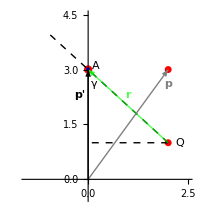

```mathematica
Plot[Sin[x],{x,- Pi/2, 4/5 Pi},PlotStyle->{White,Thickness[0.001]},PlotRange->{-.5,4.5},AspectRatio->1.1,ImageSize->200,Epilog->{Opacity[1],{Red,PointSize[0.01],Point[{2,3}]},{Red,PointSize[0.025],Point[{2,3}]},{Red,PointSize[0.03],Point[{0,3}]},{Red,PointSize[0.025],Point[{2,1}]},{Blue,PointSize[0.015],Point[{0,3}]},Arrowheads[{{.05,1}}],{Black,Dashed,Line[{{2,1},{0,1}}]},{Black,Dashed,Line[{{2,1},{-1,4}}]},{Opacity[.7],Green,Arrow[{{2,1},{0,3}}],Text[Style[r,Bold,FontSlant->Plain],{1,2.3}]},{Gray,Arrow[{{0,0},{2,3}}],Text[Style[p,Bold,FontSlant->Plain],{2,2.6}]},{Arrow[{{0,0},{0,3}}],Text[Style["p'",Bold,FontSlant->Plain],{-.2,2.3}]},{Black,Text[Style[Q,Plain],{2.3,1}]},{Black,Text["γ",{.15,2.6}]},{Black,Text[Style[A,Plain],{.2,3.1}]}}]
```

In example 3 on p. 371, the line of action of p' goes through A. I think that needs to be maintained. The vector p does not actually go through A, but there would be a component. The length of this component would be the norm of p times the cosine of the angle γ between. I could call the vector with this length and A’s direction, p'.

```mathematica
ClearAll["Global`*"]
```

```mathematica
e2={2,3}
```

{2,3}

```mathematica
e3=Norm[e2]
```

√13

```mathematica
e4=ArcTan[2/3]
```

ArcTan[2/3]

```mathematica
e5=Cos[e4]
```

3/(√13)

```mathematica
e6=e3 e5
```

3

Here is something remarkable. If I haven’t miscalculated, the vector p' is a vector terminating at A.

The length of p' is 3. The quantity mlight is the norm of mbold. Not written in the text or problem description as a norm, though just light face, not bold.

Because of the length of its sides being equal, the angle γ is seen to be π/4.

```mathematica
e7=rbold={0,3}-{2,1}
```

{-2,2}

```mathematica
e9=mbold=e7×e2
```

Cross::nonn1: The arguments are expected to be vectors of equal length, and the number of arguments is expected to be 1 less than their length.

{-2,2}×{2,3}

Above: here is where I have to put the third coordinate back in.

```mathematica
e10=mbold3={-2,2,0}×{2,3,0}
```

{0,0,-10}

```mathematica
e11=mlight=Norm[e10]
```

10

Looking down the z-axis toward the sketch of the problem, with positive x to the right, the moment mbold would tend to exert a clockwise motion around Q.

29.  Triangle. Find the area if the vertices are {0, 0, 1}, {2, 0, 5}, and {2, 3, 4}.

```mathematica
ClearAll["Global`*"]
```

```mathematica
Graphics3D[{Opacity[1],Gray,PointSize[.015],Arrowheads[{{.02,1}}],Arrow[Tube[{{0,-8,0},{0,8,0}},.01]],Arrow[Tube[{{0,0,-8},{0,0,8}},.01]],
Arrow[Tube[{{-8,0,0},{8,0,0}},.01]],Blue,Arrow[Tube[{{0,0,1},{-12,2,7}},.03]],Gray,Text["+x",{8.5,0,0}],Text["+y",{0,8.5,0}],Text["+z",{0,0,8.5}],Text["B: 2,0,5",{2.4,.4,5.4}],Text["A: 0,0,1",{0.4,0.4,1.4}],Text["C: 2,3,4",{2.4,3.4,4.4}],Dashing[Small],Line[{{0,0,1},{2,0,5}}],Line[{{2,0,5},{2,3,4}}],Line[{{0,0,1},{2,3,4}}],Line[{{2,3,4},{4,3,8}}],Line[{{2,0,5},{4,3,8}}],Red,PointSize[0.01],Point[{0,0,1}],Point[{2,0,5}],Point[{2,3,4}],Blue,PointSize[0.007],Point[{4,3,8}],Opacity[.03],Polygon[{{4,3,8},{2,0,5},{0,0,1},{2,3,4}}]},Axes->None,AxesOrigin->{0,0,0},ViewVector->{{30,30,30},{0,0,0}},ViewVertical->{0,0,1},Boxed->False,Ticks->Automatic,PlotRange->{{-30,10},{-9,9},{-9,9}},ImageSize->400,ImageMargins->0]
```

-Graphics3D-

In the sketch, I need to find the area of the triangle, ABC. Following the s.m. pretty closely, I make two vectors out of points B and C, using the common point A as their origin.

```mathematica
bbold={2-0,0-0,5-1}
```

{2,0,4}

```mathematica
cbold={2-0,3-0,4-1}
```

{2,3,3}

Then I cross these two,

```mathematica
vbold=bbold×cbold
```

{-12,2,6}

and find the norm of the cross vbold,

```mathematica
e1=Norm[vbold]
```

2 √46

The s.m. reminds me that the cross product is defined in such a way that its length is equal to the area of the base parallelogram (see sketch). Since the area of the triangle I want is exactly half the area of the parallelogram, I have,

```mathematica
e2=e1/2
```

√46

I added vbold to the sketch.

Note: Green cells in this problem set agree with the corresponding answers in the text.

31. Plane. Find the plane through (1, 3, 4), (1, -2, 6) and (4, 0, 7).

```mathematica
ClearAll["Global`*"]
```

```mathematica
Subscript[v, 1]={1,3,4}
```

{1,3,4}

```mathematica
Subscript[v, 2]={1,-2,6}
```

{1,-2,6}

```mathematica
Subscript[v, 3]={4,0,7}
```

{4,0,7}

```mathematica
perp=Cross[Subscript[v, 2]-Subscript[v, 1],Subscript[v, 2]-Subscript[v, 3]]
```

{9,-6,-15}

```mathematica
Simplify[9(x-1)-6(y+2)-15(z-6)==0]
```

23+3 x==2 y+5 z

The equation in the yellow cell does not match the answer in the text. However, it does check with the answer put forth by WolframAlpha.

33. Tetrahedron. Find the volume if the vertices are (1, 1, 1), (5, -7, 3), (7, 4, 8), and (10, 7, 4).

```mathematica
ClearAll["Global`*"]
```

Taking a tip from Weisstein’s MathWorld, the volume should be

```mathematica
A=({{1, 1, 1, 1}, {5, -7, 3, 1}, {7, 4, 8, 1}, {10, 7, 4, 1}})
```

{{1,1,1,1},{5,-7,3,1},{7,4,8,1},{10,7,4,1}}

```mathematica
volume=1/(3!)Det[A]
```

79

The answer in the green cell above matches that of the text.